```mathematica
SetDirectory["/Volumes/MicroSD/Dropbox/PostDoc_SD/ZrC/Thermodynamic_Integration_Analysis/UP_sample"];
teldData=ReadList["T0.1_T0.328eV_eltempdiff.dat",{Number, Number,Number,Number}];
eVcel2meVatom=1000/64;
(*F 0.1 E0 0.1 then F 0.328 E0 0.328*)
```

```mathematica
f01=eVcel2meVatom*(Transpose[teldData][[1]]-teldData[[1]][[1]]);
e001=eVcel2meVatom*(Transpose[teldData][[2]]-teldData[[1]][[2]]);
f03=eVcel2meVatom*(Transpose[teldData][[3]]-teldData[[1]][[3]]);
e003=eVcel2meVatom*(Transpose[teldData][[4]]-teldData[[1]][[4]]);
```

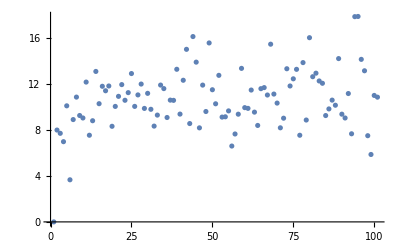

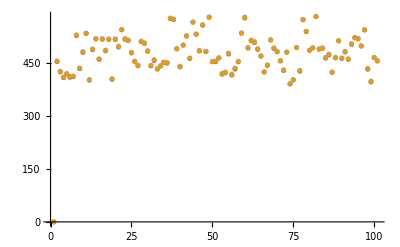

```mathematica
ListPlot[{f01-f03}]
ListPlot[{e001,e003}]
```

```mathematica
sds=Table[StandardDeviation[{f01,e001,f03,e003}[[i]]],{i,1,4}]
means=Table[Mean[{f01,e001,f03,e003}[[i]]],{i,1,4}]
```

{66.5221,66.692,64.8313,66.5811}

{474.15,474.848,463.481,476.036}

```mathematica
"UP-sample an MDrun with 0.1 and 0.328 eV electron temperatures"
"Data : {0.1eV Free, 0.1eV E0, 0.328 eV Free, 0.328 eV E0}"
sds
means
```

UP-sample an MDrun with 0.1 and 0.328 eV electron temperatures

Data : {0.1eV Free, 0.1eV E0, 0.328 eV Free, 0.328 eV E0}

{66.5221,66.692,64.8313,66.5811}

{474.15,474.848,463.481,476.036}

```mathematica
means[[1]]-means[[3]]
means[[2]]-means[[4]]
```

10.6686

-1.18735

```mathematica
means[[1]]-means[[2]]
means[[3]]-means[[4]]
```

-0.698492

-12.5545

```mathematica
means[[3]]-means[[4]]
means[[1]]-means[[4]]
```

-12.5545

-1.88585

```mathematica
means[[1]]-means[[4]]
means[[1]]-means[[3]]
```

-1.88585

10.6686

-Graphics-

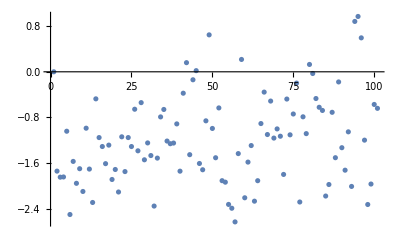

```mathematica
ListPlot[f01-f03]
ListPlot[e001-e003]
```